# Loading Initial Data

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
str=OpenRead["results_order2_slice0.bin",{BinaryFormat->True}]
rawFile0= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse\2) Analytical Scale\Export

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice1.bin",{BinaryFormat->True}]
rawFile1= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice2.bin",{BinaryFormat->True}]
rawFile2= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
str=OpenRead["results_order2_slice3.bin",{BinaryFormat->True}]
rawFile3= BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
Close[str];
```

InputStream[…]

```mathematica
(* Organize raw list into a proper 2D array depending on suface's theta/roughness *)
resX=20;
resY=10;
table0=Table[rawFile0[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table1=Table[rawFile1[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table2=Table[rawFile2[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
table3=Table[rawFile3[[1+(20*j)+i]],{j,0,resY-1},{i,0,resX-1}];
MatrixForm[table0];
```

```mathematica
table0[[10,20]]
```

{0.,1.,1.×10^-6,0.21592,0.}

## Fitting Lobe Roughness

```mathematica
paramsAlpha0 = Table[table0[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsAlpha1 = Table[table1[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsAlpha2 = Table[table2[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
paramsAlpha3 = Table[table3[[j]][[i]][[2]],{j,1,resY},{i,1,resX}];
MatrixForm[paramsAlpha0];
ListPlot3D[paramsAlpha0,{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
```

-Graphics3D-

```mathematica
roughness2exponent[α_] := 2^(10*(1-α))-1
roughness2exponent[0.95913]
```

0.327489

```mathematica
ListPlot3D[roughness2exponent[paramsAlpha0],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}]
ListPlot3D[roughness2exponent[paramsAlpha1],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}];
ListPlot3D[roughness2exponent[paramsAlpha2],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}];
ListPlot3D[roughness2exponent[paramsAlpha3],{ColorFunction->Red,ColorFunctionScaling->False, PlotRange->{0,1.2}}];
```

-Graphics3D-

It would seem that, ignoring the last 2 or 3 rows of each array, we have quite a uniform roughness.
Averaging roughnesses we obtain:

```mathematica
avgAlpha0 = Sum[paramsAlpha0[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3))
avgAlpha1 = Sum[paramsAlpha1[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3));
avgAlpha2 = Sum[paramsAlpha2[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3));
avgAlpha3 = Sum[paramsAlpha3[[j]][[i]],{i,1,resX},{j,1,resY-3}] / (resX * (resY-3));
```

0.918443

```mathematica
avgExponent0=roughness2exponent[avgAlpha0]
avgExponent1=roughness2exponent[avgAlpha1];
avgExponent2=roughness2exponent[avgAlpha2];
avgExponent3=roughness2exponent[avgAlpha3];
```

0.759995

So we could use an average exponent of 0.7, maybe 0.5 so we could simply take the square root of the cosine term?

## Assumptions

We assume that roughness α is independent of albedo and cos(θ), despite the deep holes we can see at θ = 0 and θ = π/2.
We also ignore the deep crevice when roughness α→0 because of simulation precision with small lobes and assume instead a continuity of the slope tendency.
By averaging together several slices from the valid θ range we obtain:

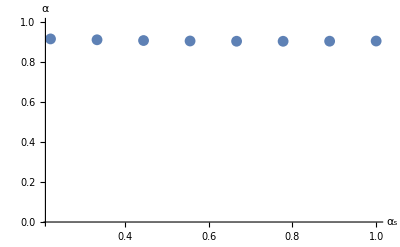

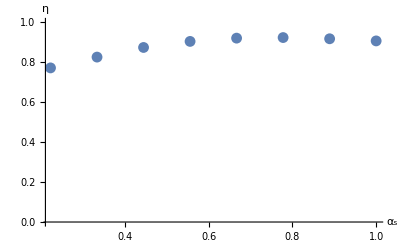

```mathematica
valuesAlpha = Table[{1-(j-1)/(resY-1),1/15 Sum[paramsAlpha0[[j]][[i]],{i,3,17}]},{j,1,8}];
valuesEta = Table[{1-(j-1)/(resY-1),roughness2exponent[1/15 Sum[paramsAlpha0[[j]][[i]],{i,3,17}]]},{j,1,8}];
ListPlot[valuesAlpha,PlotRange->{0,1},AxesLabel->{"α_s","α"}]
ListPlot[valuesEta,PlotRange->{0,1},AxesLabel->{"α_s","η"}]
```

I’d really like to fit an interesting curve here but it really would seem the average roughness is roughly a constant...

FittedModel[0.916894-0.0130917 x]

FittedModel[0.778289+0.168317 x]

0.778289

0.168317

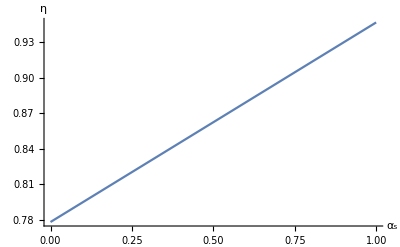

```mathematica
LinearModelFit[Table[1/15 Sum[paramsAlpha0[[j]][[i]],{i,3,17}],{j,1,8}]];
fit =LinearModelFit[valuesAlpha,x,x]
fit =LinearModelFit[valuesEta,x,x]
fit[[1]][[2]][[1]]
fit[[1]][[2]][[2]]
Plot[fit[x],{x,0,1},AxesLabel->{"α_s","η"}]
```

0.916894-0.0130917 α

0.778289+0.168317 α

0.916894

0.903802

0.778289

0.946607

0.778996

0.947982

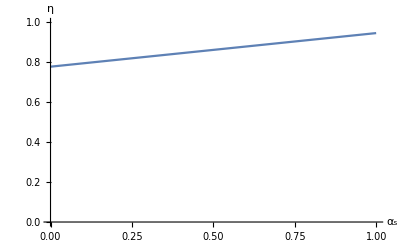

```mathematica
Clear[α]
roughness[α_]=0.9168937073335606-0.013091709358763996α
exponent[α_]=0.7782894918463 + 0.1683172467667511α
roughness[0]
roughness[1]
exponent[0]
exponent[1]
roughness2exponent[roughness[0]]
roughness2exponent[roughness[1]]
Plot[exponent[α],{α,0,1},PlotRange->{0,1},AxesLabel->{"α_s","η"}]
```

Matching Masking Importance

```mathematica
paramsMask0 = Table[table0[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask1 = Table[table1[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask2 = Table[table2[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
paramsMask3 = Table[table3[[j]][[i]][[5]],{j,1,resY},{i,1,resX}];
```

```mathematica
ListPlot3D[paramsMask0,{ PlotRange->{0,0.25},AxesLabel->{"θ","ρ"}}]
ListPlot3D[paramsMask1,{ PlotRange->{0,0.25},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsMask2,{ PlotRange->{0,1},AxesLabel->{"θ","ρ"}}];
ListPlot3D[paramsMask3,{ PlotRange->{0,1},AxesLabel->{"θ","ρ"}}];
```

-Graphics3D-

And it would seem that masking is globally 0... Which is a good thing!